# 2: Orthogonal Vectors and Matrices

## Adjoint, Inner Product and Norm

For an m×n matrix A the adjoint A^* is the n×m matrix obtained by interchanging rows and columns of the complex conjugate of A.  In other words
	(A^*)_(i,j)=(Ā)_(j,i)

ℂ^m comes with an inner product
	<x,y> =x̄.y=∑_(j=1)^m ((x̄)_j y_j)
which is just the familiar calculus inner product if we are in ℝ^m.   The norm is just ||x||=√(<x.x>).  In ℝ^m we have the familiar formula for the angle α between two vectors 
	Cos[α]=(<x.y>)/(||x||||y||)
Warning, if x and y are single column matrices then <x,y> =x^*.y which is a common matlab syntax.  Other software defines and stores vectors as vectors rather than extremely skinny matrices.

You can compute it in Mathematica with “.”.  If you like working harder you can build it from the recipe.

```mathematica
m=4;
{x,y}=RandomComplex[{-1-I,1+I},{2,m}];
{Conjugate[x].y,Sum[Conjugate[x⟦i⟧]*y⟦i⟧,{i,m}]}
{√(Conjugate[x].x),Norm[x]}
```

{-0.596481+0.476064 ⅈ,-0.596481+0.476064 ⅈ}

{1.70542+0. ⅈ,1.70542}

## Outer Product of Vectors

The outer product x⊗y of a vector x∈ℝ^m and a vector y∈ℝ^n is the m×n matrix with entries 
	 (x⊗y)_(i,j)=x_i y_j.
You can form it in Mathematica with the command KroneckerProduct.  If you like working harder you can build it from the recipe.

```mathematica
{m,n}={3,2};
x=RandomReal[{-1,1},m];
y=RandomReal[{-1,1},n];
TabView[{
MatrixForm[KroneckerProduct[x,y]],
MatrixForm[Table[x⟦i⟧y⟦j⟧,{i,m},{j,n}]]}]
```

12

ℂ^m comes with an inner product
	<x,y> =x̄.y=∑_(j=1)^m ((x̄)_j y_j)
which is just the familiar calculus inner product if we are in ℝ^m.   The norm is just ||x||=√(<x.x>).  In ℝ^m we have the familiar formula for the angle α between two vectors 
	Cos[α]=<x.y>(<x.y>)/(||x||||y||)
Warning, if x and y are single column matrices then <x,y> =x^*.y which is a common matlab syntax.  Other software defines and stores vectors as vectors rather than extremely skinny matrices.

```mathematica
m=4;
{x,y}=RandomComplex[{-1-I,1+I},{2,m}];
{Conjugate[x].y,Sum[Conjugate[x⟦i⟧]*y⟦i⟧,{i,m}]}
{√(Conjugate[x].x),Norm[x]}
```

{0.577437+0.0104325 ⅈ,0.577437+0.0104325 ⅈ}

{1.27914+0. ⅈ,1.27914}

## Orthogonality: Vectors and Matrices

Two vectors x and y are orthogonal if <x,y> =0. 
An m×m matrix Q is unitary (orthogonal for real Q) if Q^*=Q^-1.
Since Q^*.Q=Id this means that the columns of Q are orthogonal (off-diagonals) and each column has norm 1 (diagonals).   The QR decomposition (available in every computational tool) gives an orthogonal matrix Q.

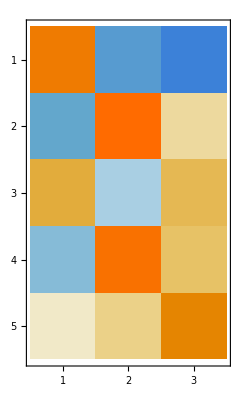
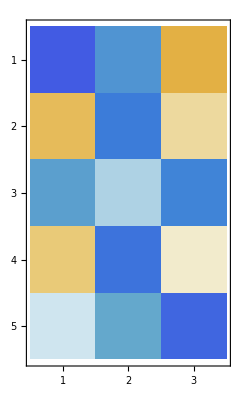
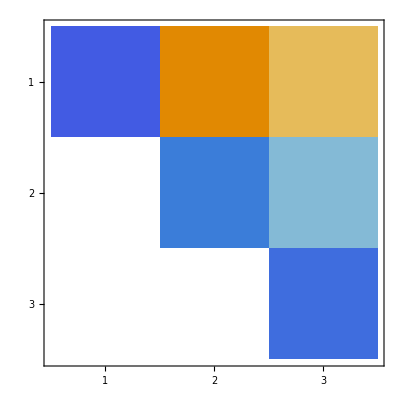
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{m,n}={5,3};
A=RandomReal[{-1,1},{m,n}];
{Q,R}=QRDecomposition[A]; Q=Qᵀ; (* Mathematica gives rows instead of columns *)
Norm[ Qᵀ.Q-IdentityMatrix[n]];
Map[MatrixPlot,{A,Q.R,Q,R}]
```

Orthogonal matrices Q preserve lengths of vectors and the angles between vectors. From ℝ^m→ℝ^m they are rotations or reflections and folks use this terminology.  They are the fundamental building block of modern NLA!

```mathematica
{x,y}=RandomReal[{-1,1},{2,m}];
{{Norm[x], Norm[Q.x]},{(x.y),(Q.x).(Q.y)}}
```

{{1.05094,1.05094},{-0.438341,-0.438341}}

## Orthogonal Matrix Families

We will see how to make “orthogonalize” a matrix!  But it is convenient to have “automatically” orthogonal square matrices.  The world calls orthogonal matrices Q

### Givens Rotation: G2

Suppose p_1^2+p_2^2=1 and i1≠i2 then we can build an orthogonal m×m matrix Q as follows.

```mathematica
m=7;
{i1,i2}={4,2};
{p1,p2}=Normalize[RandomReal[{-1,1},2]]
Q=SparseArray[{
{{i1,i1},{i2,i2}}->p1,
{i1,i2}->p2,{i2,i1}->-p2,
Band[{1,1}]->1},{m,m}];
MatrixForm[Q]
Norm[Qᵀ.Q-IdentityMatrix[m]]
```

{-0.373244,-0.927733}

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.373244 | 0 | 0.927733 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | -0.927733 | 0 | -0.373244 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

2.41069×10^-16

How do we check this claim? Is the 2×2 submatrix in the {i,j} entries familiar? Does it help if we call p_1=Cos[θ] and p_2=Sin[θ]?

### Givens Rotation: G4

Suppose p={p_1,p_2,p_3,p_4} satisfies ||p||=1 and the none of the indices {i1,i2,i3,i4} are repeated then we can build an orthogonal m×m matrix Q as follows.

```mathematica
m=7;
{i1,i2,i3,i4}={1,3,5,6};
{p1,p2,p3,p4}=Normalize[RandomReal[{-1,1},4]];
Q=IdentityMatrix[m];
Q⟦{i1,i2,i3,i4},{i1,i2,i3,i4}⟧=({{p1, -p2, -p3, -p4}, {p2, p1, -p4, p3}, {p3, p4, p1, -p2}, {p4, -p3, p2, p1}});
MatrixForm[Q]
Norm[Qᵀ.Q-IdentityMatrix[m]]
```

(0.191419 | 0 | 0.546304 | 0 | -0.776653 | -0.248438 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
-0.546304 | 0 | 0.191419 | 0 | -0.248438 | 0.776653 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0.776653 | 0 | 0.248438 | 0 | 0.191419 | 0.546304 | 0
0.248438 | 0 | -0.776653 | 0 | -0.546304 | 0.191419 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

6.93889×10^-18

### Givens Rotation: G8

Suppose p∈ℝ^8 satisfies ||p||=1 and the none of the indices i∈ℤ_8^+ are repeated then we can build an orthogonal m×m matrix Q as follows.

```mathematica
m=12;
i={2,3,4,5,6,7,8,9};
{p1,p2,p3,p4,p5,p6,p7,p8}=Normalize[RandomReal[{-1,1},8]];
Q=IdentityMatrix[m];
Q⟦i,i⟧=({{p1, p2, p3, p4, p5, p6, p7, p8}, {-p2, p1, p4, -p3, p6, -p5, -p8, p7}, {-p3, -p4, p1, p2, p7, p8, -p5, -p6}, {-p4, p3, -p2, p1, p8, -p7, p6, -p5}, {-p5, -p6, -p7, -p8, p1, p2, p3, p4}, {-p6, p5, -p8, p7, -p2, p1, -p4, p3}, {-p7, p8, p5, -p6, -p3, p4, p1, -p2}, {-p8, -p7, p6, p5, -p4, -p3, p2, p1}});
MatrixForm[Q]
Norm[Qᵀ.Q-IdentityMatrix[m]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.414091 | 0.343748 | 0.019988 | -0.402248 | 0.460148 | 0.285961 | -0.500378 | 0.0653793 | 0 | 0 | 0
0 | -0.343748 | 0.414091 | -0.402248 | -0.019988 | 0.285961 | -0.460148 | -0.0653793 | -0.500378 | 0 | 0 | 0
0 | -0.019988 | 0.402248 | 0.414091 | 0.343748 | -0.500378 | 0.0653793 | -0.460148 | -0.285961 | 0 | 0 | 0
0 | 0.402248 | 0.019988 | -0.343748 | 0.414091 | 0.0653793 | 0.500378 | 0.285961 | -0.460148 | 0 | 0 | 0
0 | -0.460148 | -0.285961 | 0.500378 | -0.0653793 | 0.414091 | 0.343748 | 0.019988 | -0.402248 | 0 | 0 | 0
0 | -0.285961 | 0.460148 | -0.0653793 | -0.500378 | -0.343748 | 0.414091 | 0.402248 | 0.019988 | 0 | 0 | 0
0 | 0.500378 | 0.0653793 | 0.460148 | -0.285961 | -0.019988 | -0.402248 | 0.414091 | -0.343748 | 0 | 0 | 0
0 | -0.0653793 | 0.500378 | 0.285961 | 0.460148 | 0.402248 | -0.019988 | 0.343748 | 0.414091 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

1.32873×10^-16

### Block Matrices

We can build a big matrix out of a grid of smaller conforming matrices

```mathematica
m=5;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
B1=ArrayFlatten[{
{A,0},
{0,A}}];
B2=ArrayFlatten[({{0, A}, {A, 0}})];
TabView[{
"B"->TabView[Map[MatrixPlot,{B1,B2}]],
"λ(B)"->TabView[Map[Eigenvalues,{B1,B2}]]
}]
```

12

### Projections and Householder Reflectors

For a unit vector v the matrix 
	P=I- v⊗v
is a Projector!

```mathematica
m=24;
v=Normalize[RandomReal[{-1,1},m]];
P=IdentityMatrix[m]- KroneckerProduct[v,v];
MatrixPlot[P];
Norm[P.P-P]
Eigenvalues[P]
```

2.22886×10^-16

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,9.71445×10^-17}

For a unit vector v the matrix 
	H=I-2 v⊗v
is orthogonal!

```mathematica
m=4;
v=Normalize[RandomReal[{-1,1},m]];
H=IdentityMatrix[m]-2 KroneckerProduct[v,v];
Norm[Hᵀ.H-IdentityMatrix[m]]
```

7.30904×10^-16